## Bayesian Statistics, Assignment for Friday, Nov. 1

## Reading

Study to the end of Chapter 6 of our Bayesian statistics book.

## Review/Overview

On the last day before break, to give you an idea where we will be heading soon, I derived the following Bayes theorem for a continuum of hypotheses, specified by a continuous parameter, a.

P(a^*|O)Δ a^*=(P(O|a^*)P(a^*)Δ a^*)/(∫_a_min^a_max P(O|a)P(a)da)

We worked pretty hard to get that formula, and I don’t yet expect you to fully comprehend it! I’m just reminding you of it so you can keep it in the back of your mind as you do this assignment.

What is going on in Chapter 6? It is warming you up to formulas like the above! You have seen binary hypotheses (Hamilton or not Hamilton). You have seen ternary hypotheses (is a rock, is a potato, or is a rotten turnip). Now in Chapter 6, you are seeing twelve hypotheses (happened in Jan, happened in Feb, happened in Mar, etc.). When you make a histogram with 12 bins, does it not start to look like a function? If you had 144 hypotheses, or 1728 hypotheses, and imagined what a histogram would look like with 144 or 1728 bins, then isn’t it starting to look even more like a continuous function?

The bottom line is that in Chapter 6, we are starting to build our intuition for a continuum of hypotheses by jumping to 12 mutually exclusive hypotheses. Bayes theorem for 12 mutually-exclusive hypotheses, numbered from 1 to 12 is:

P(i|O)=(P(O|i)P(i))/(∑_(j=1)^12 P(O|j)P(j))

## For Problem Set 10 — The Mudslide Problem

In the authors’ example in Chapter 6, Mary can be born in Jan, Feb, Mar, ..., Dec. These are the 12 mutually exclusive hypotheses. I very much like the authors’ jump to 12 mutually exclusive hypotheses, but I found the story about determining Mary’s birthday contrived. So instead of the birthday problem, I made up this mudslide problem.

### The Mudslide Problem

Imagine that a prehistoric mudslide is being excavated, and you are a geologist or a palynologist, and you are trying to figure out what month of the year the mudslide is likely to have occurred.

### Step 1 — Tabulating the Prior

As the prior, we will use this lovely plot of mudslide frequencies by month:

Convert the mudslide frequency plot above to a table. You can keep it in percentages or you can convert it to decimal form. E.g., 0.5% would become 0.005.

```mathematica
months = {"Jan","Feb","Mar", "Apr", "May", "Jun", "Jul", "Aug", "Sep", "Oct", "Nov", "Dec"};TableForm[Table["", {i, 0, 11}, {j, 1, 1}], TableHeadings->{months,{"Prior P(i)"}}]
```

| Prior P(i)
Jan | 
Feb | 
Mar | 
Apr | 
May | 
Jun | 
Jul | 
Aug | 
Sep | 
Oct | 
Nov | 
Dec |

### Step 2 — Tabulating the Likelihoods

As the observation, O, we will imagine that we looked for and identified two kinds of pollen in the prehistoric mud: Ambrosia pollen and Gramineae / Poaceae pollen. In fact, upon looking for these two kinds of pollen, our observation is that the concentration of Ambrosia pollen is higher than the concentration of Gramineae / Poaceae pollen. Examining historical pollen records, in locations where both Ambrosia and Gramineae / Poaceae pollen are found, generally speaking the only months of the year that Ambrosia outnumbers Gramineae / Poaceae are August, September, October, and November (with a possible exception to this rough generality in April). Below are the actual modern records for pollen counts for various species near Waco, Texas. (To be frank, the mudslide frequencies in Step 1 came from Uzbekistan, but let’s pretend that the data all comes from the same location.)

After studying this beautiful graphic, make an estimate for each month that  Ambrosia outnumbers Gramineae / Poaceae for that month. Use the estimates to fill in the table on the next page.

```mathematica
TableForm[Table["", {i, 0, 11}, {j, 1, 1}], TableHeadings->{months,{"Likelihood P(O|i)"}}]
```

| Likelihood P(O|i)
Jan | 
Feb | 
Mar | 
Apr | 
May | 
Jun | 
Jul | 
Aug | 
Sep | 
Oct | 
Nov | 
Dec |

If you are a tad confused about what I am asking, let me tell you how I would estimate April. It looks like there are 1 or 2 days in April that Ambrosia pollen was observed and the color in the plot makes it look like the pollen concentration was around 30-100  grains / m^3 on those two days. Meanwhile, in April, the Gramineae / Poaceae concentration was equally strong or stronger on all of the other days in April, so I am going to make as my estimate of the likelihood:

P(Ambrosia concentration is higher than Gramineae / Poaceae | April) = 1 /30.

If you look at the same data and get 2/30 or 0/30, for your likelihood, it will of course change the posterior a little. Just do your best. Note that unlike the priors, the likelihoods do not have to add up to 1.

### Step 3 — Tabulating the Products

To make it less likely that we will flub up, as a separate step before calculating the posteriors, let’s tabulate all 12 products we will be using:

```mathematica
TableForm[Table["", {i, 0, 11}, {j, 1, 1}], TableHeadings->{months,{"Product P(O|i) * P(i)"}}]
```

| Product P(O|i) * P(i)
Jan | 
Feb | 
Mar | 
Apr | 
May | 
Jun | 
Jul | 
Aug | 
Sep | 
Oct | 
Nov | 
Dec |

### Step 4 — Computing the Sum

To finish getting the denominator in  P(i|O)=(P(O|i)P(i))/(∑_(j=1)^12 P(O|j)P(j)), compute


∑_(j=1)^12 P(O|j)P(j)=

### Step 5 — Computing the Posteriors

Now that you have done steps 1 to 4 it should be hardly any work at all to compute the posteriors:

```mathematica
TableForm[Table["", {i, 0, 11}, {j, 1, 1}], TableHeadings->{months,{"Posterior P(i|O)"}}]
```

| Posterior P(i|O)
Jan | 
Feb | 
Mar | 
Apr | 
May | 
Jun | 
Jul | 
Aug | 
Sep | 
Oct | 
Nov | 
Dec |

As a double-check on your computations, make sure that the posteriors add up to 1, or if you converted them to percentages, to 100%.

### Step 6 — Plotting the Posteriors

The mudslide problem began with a lovely plot of the prior:

On the next page, make a lovely plot of the posteriors using your table from Step 5. For readability of the table, convert back to percentages if you haven’t already.

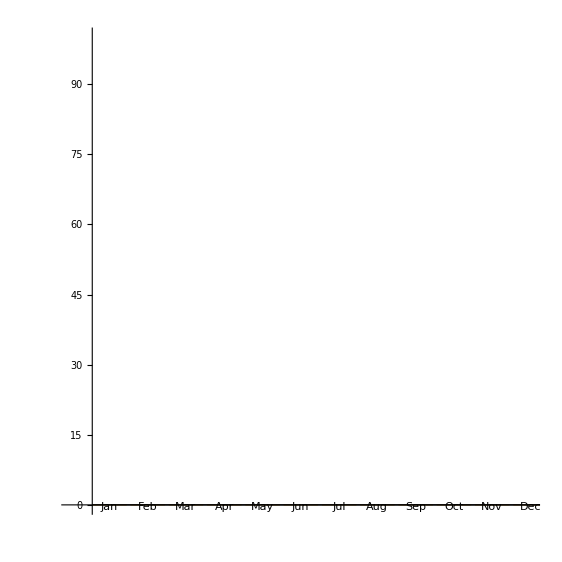

```mathematica
BarChart[Table[0, {j, 1, 12}], PlotRange->{{0, 12},{0, 100}}, ChartLabels->months, PlotRangePadding->1.0, FrameLabel->{"Posterior (%)"}, AspectRatio->1, ImagePadding->50]
```